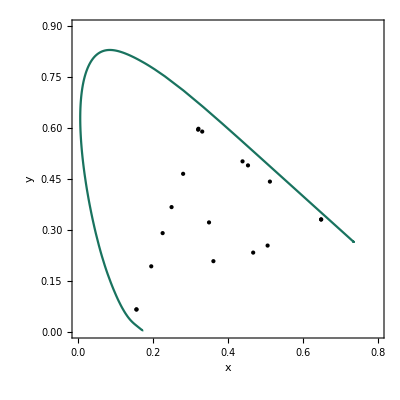

```mathematica
ChromaticityPlot[res2[18][[2]],Appearance->"VisibleSpectrum",PlotStyle->Black]
```

```mathematica
ChromaticityPlot[{{RGBColor[{0.16979999268824753, 0.4698443189004301, 0.6181391010268967}],RGBColor[{0.2029488783649783, 0.48375572337353023, 0.43862436689563483}],RGBColor[{0.5667584159651767, 0.39420846590787983, 0.32816926078505937}],RGBColor[{0.5567186090541492, 0.4093890807692052, 0.012711977055572999}],RGBColor[{0.4338558696441102, 0.40874707064547505, 0.679542930259959}],RGBColor[{0.6773013913001884, 0.2671013959328433, 0.6868801022446491}],RGBColor[{0.4063004683142298, 0.4563592127276685, 0.27148430588833505}],RGBColor[{0.43352538092594284, 0.4368511416077785, 0.4502943845582339}],RGBColor[{0.7459663829388814, 0.2529806830990633, 0.39979548521422453}]},"RGB"},"CIE76",Appearance->"VisibleSpectrum"]
```

-Graphics-

```mathematica
%512[[2,2]]
```

{r[1]→0.0085041,g[1]→0.595592,b[1]→0.615846,r[2]→3.47427×10^-10,g[2]→0.619806,b[2]→8.96652×10^-11,r[3]→0.919444,g[3]→0.014443,b[3]→0.999855,r[4]→0.996883,g[4]→0.142403,b[4]→0.47312,r[5]→0.726129,g[5]→0.474305,b[5]→0.0390624,r[6]→0.372398,g[6]→0.510247,b[6]→0.991965,l→0.56613}

```mathematica
resVe[5]
```

{41.396,{RGBColor[{0.9552705621364173, 0.0004508236834875069, 0.594769450198664}],RGBColor[{0.43910524277033064, 0.450886810238386, 0.9999999901503588}],RGBColor[{0.5837075085975266, 0.49899803629000594, 7.062649992952563*^-18}],RGBColor[{0.9940359279958006, 0., 0.00013529919093111027}],RGBColor[{0.023611292174193367, 0.563261792884507, 0.6134410975565231}]}}

```mathematica
resV[5]
```

{35.228,{RGBColor[{0.8002054949736606, 0.3951355682562587, 0.5863736429277759}],RGBColor[{0.12395639425632092, 0.5882083536538333, 0.660249306463808}],RGBColor[{0.00010637038853234383, 0.6194017418450074, 0.1076592115562757}],RGBColor[{0.7181993874960064, 0.4793138933137573, 0.}],RGBColor[{0.9218965834375517, 0., 0.9999999900042031}]}}

```mathematica
resL[5]
```

{46.684,{RGBColor[{0.770705000974634, 0., 0.9999999890273601}],RGBColor[{4.810341362199771*^-11, 0.5194230011258653, 0.5742892804241732}],RGBColor[{0., 0.5438813376285707, 0.}],RGBColor[{2.991857602907742*^-11, 0.4521228972858653, 0.999999991178841}],RGBColor[{0.9201074243470475, 0., 0.}]}}

```mathematica
ColorDistance[LABColor[.5,.9,-1.5],RGBColor[{0.770705000974634, 0., 0.9999999890273601}]]
```

0.727791

```mathematica
LABColor[.5,.9,-1.5]
```

LABColor[0.5, 0.9, -1.5]

```mathematica
tol=.02;
lev=0.4700708218952139;
tol2=.01;
```

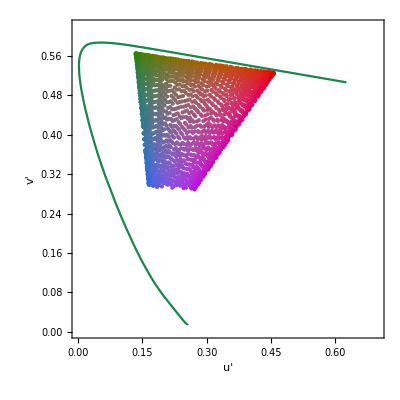

```mathematica
ChromaticityPlot[Select[Flatten[Table[RGBColor[r,g,b],{r,0,1,tol},{g,0,1,tol},{b,0,1,tol}]],lev-tol2<ColorConvert[#,"LAB"][[1]]<lev+tol2&],"CIE76",Appearance->"VisibleSpectrum"]
```

```mathematica
L/@(trips/.%690[[2,2]])
```

{0.460548,0.460548,0.460548,0.460548,0.460548,0.460548,0.460548,0.460548,0.460548}

```mathematica
cost/.%690[[2,2]]
```

-0.223333

```mathematica
Timing[NMinimize[{cost,cons},Join[Join@@trips,{l}],MaxIterations->300,AccuracyGoal->9,PrecisionGoal->8]]
```

{341.752,{-0.223333,{r[1]→0.239593,g[1]→0.449915,b[1]→0.615092,r[2]→0.0402115,g[2]→0.482917,b[2]→0.443956,r[3]→0.625,g[3]→0.353443,b[3]→0.201492,r[4]→0.497648,g[4]→0.420617,b[4]→0.00215736,r[5]→0.448007,g[5]→0.40977,b[5]→0.538626,r[6]→0.718977,g[6]→0.167378,b[6]→0.734249,r[7]→0.17701,g[7]→0.488828,b[7]→0.142572,r[8]→0.426182,g[8]→0.430618,b[8]→0.396706,r[9]→0.7073,g[9]→0.274738,b[9]→0.376836,l→0.460548}}}

```mathematica
{%[[1]],RGBColor/@(trips/.%[[2,2]])}
```

{341.752,{RGBColor[{0.23959288000720846, 0.4499147599136932, 0.615092059739195}],RGBColor[{0.0402115042986185, 0.4829172979562427, 0.44395597396791503}],RGBColor[{0.6250004798542579, 0.35344340819187736, 0.20149193778967198}],RGBColor[{0.49764759744518583, 0.42061740239124057, 0.0021573641777771746}],RGBColor[{0.4480070002498887, 0.40976970144793073, 0.5386263928752592}],RGBColor[{0.7189767353032925, 0.1673780951692489, 0.7342494259150166}],RGBColor[{0.1770104555257851, 0.48882750229178173, 0.14257221752139318}],RGBColor[{0.4261816209209114, 0.43061807131906404, 0.3967060451518484}],RGBColor[{0.707300380442856, 0.27473751100782384, 0.3768355007568552}]}}

```mathematica
Timing[NMinimize[{cost,cons},Join[Join@@trips,{l}],MaxIterations->300,AccuracyGoal->9,PrecisionGoal->8]]
```

{306.412,{-0.20073,{r[1]→0.1698,g[1]→0.469844,b[1]→0.618139,r[2]→0.202949,g[2]→0.483756,b[2]→0.438624,r[3]→0.566758,g[3]→0.394208,b[3]→0.328169,r[4]→0.556719,g[4]→0.409389,b[4]→0.012712,r[5]→0.433856,g[5]→0.408747,b[5]→0.679543,r[6]→0.677301,g[6]→0.267101,b[6]→0.68688,r[7]→0.4063,g[7]→0.456359,b[7]→0.271484,r[8]→0.433525,g[8]→0.436851,b[8]→0.450294,r[9]→0.745966,g[9]→0.252981,b[9]→0.399795,l→0.470071}}}

```mathematica
{%[[1]],RGBColor/@(trips/.%[[2,2]])}
```

{306.412,{RGBColor[{0.16979999268824753, 0.4698443189004301, 0.6181391010268967}],RGBColor[{0.2029488783649783, 0.48375572337353023, 0.43862436689563483}],RGBColor[{0.5667584159651767, 0.39420846590787983, 0.32816926078505937}],RGBColor[{0.5567186090541492, 0.4093890807692052, 0.012711977055572999}],RGBColor[{0.4338558696441102, 0.40874707064547505, 0.679542930259959}],RGBColor[{0.6773013913001884, 0.2671013959328433, 0.6868801022446491}],RGBColor[{0.4063004683142298, 0.4563592127276685, 0.27148430588833505}],RGBColor[{0.43352538092594284, 0.4368511416077785, 0.4502943845582339}],RGBColor[{0.7459663829388814, 0.2529806830990633, 0.39979548521422453}]}}

```mathematica
cost/.%714[[2,2]]
```

-0.20073

```mathematica
cost/.{r[1]->0.16979999268824753,g[1]->0.4698443189004301,b[1]->0.6181391010268967,r[2]->0.2029488783649783,g[2]->0.48375572337353023,b[2]->0.43862436689563483,r[3]->0.5667584159651767,g[3]->0.39420846590787983,b[3]->0.32816926078505937,r[4]->0.5567186090541492,g[4]->0.4093890807692052,b[4]->0.012711977055572999,r[5]->0.4338558696441102,g[5]->0.40874707064547505,b[5]->0.679542930259959,r[6]->0.6773013913001884,g[6]->0.2671013959328433,b[6]->0.6868801022446491,r[7]->0.4063004683142298,g[7]->0.4563592127276685,b[7]->0.27148430588833505,r[8]->0.43352538092594284,g[8]->0.4368511416077785,b[8]->0.4502943845582339,r[9]->.8653,g[9]->0.,b[9]->0.,l->0.4700708218952139}
```

-0.201026

```mathematica
l/.%714[[2,2]]
```

0.470071

```mathematica
Table[L[N@{x,0,0}],{x,.865,.866,.0001}]
```

{0.469988,0.470043,0.470097,0.470152,0.470207,0.470262,0.470317,0.470371,0.470426,0.470481,0.470536}